# Plane-strain Star Crack

```mathematica
PacletDirectoryLoad[(*NotebookDirectory[]<>*)"/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/interfaces/mathematica/"]
<<BigWhamLink`
$BigWhamVersion
GetFilesDate[]
```

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/interfaces/mathematica/}

WARNING: LTemplate has not yet been tested with Mathematica 13.2.0.
The latest supported Mathematica version is 12.1.1.
Please report any issues you find to szhorvat at gmail.com.

BigWhamLink`LTemplate`Classes`

1.2.2

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/interfaces/mathematica/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Mon 13 Feb 2023 18:57:08GMT+1,/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a→Mon 13 Feb 2023 18:51:18GMT+1}

## Analytical Solution of a star Crack

M . Stallybrass . A cruciform crack deformed by an arbitrary internal pressure . International Journal of Engineering Science, 7 (11) : 1103–1116, 1969.

M. P. Stallybrass. a pressurized crack in the form of a cross. The Quarterly Journal of Mechanics and Applied Mathematics, 23(1):35–48, 1970.

```mathematica
ElasProp=<|"YM"-> 2.4,"nu"-> 0.2|>;
```

```mathematica
Ep=ElasProp["YM"]/(1-ElasProp["nu"]^2)
```

2.5

```mathematica
(* n indicate the number of cracks *)
Iw[n_]:=NIntegrate[Log[1+Tan[x]Sin[(2π)/n]Csch[(2π)/n Tan[x]]],{x,0,π/2}];
KK[n_]:=2^(1-2/n)√(1/n)Exp[-1/π Iw[n]];
KIw[n_]:=√(2π)KK[n];
Ww[n_]:=n π KK[n]^2;
v0w[n_]:=(2 √n Sin[π/n])/(√(1+n/(2π)Sin[(2π)/n]))KK[n];

KIref[n_]:=Pnet √a KIw[n];
KIIref=0.;
Wref[n_]:=(Pnet^2 a^2)/Ep Ww[n];
Aref[n_]:=(2Wref[n])/Pnet;
w0ref[n_]:=2(Pnet a)/Ep v0w[n];
(* approximation small n *)
GO[n_]:=2. √(1-1/n);
GT[n_]:=2.-1.050 1/n-0.243 1/n^2;
Glim=2.;
G[n_,ind_]=If[ind==1,GO[n],If[ind==2,GT[n],Glim]];
KIapp[n_,ind_]=(Pnet √(π a))/(√n)G[n,ind];
Aapp[n_,ind_]=(Pnet π a^2)/Ep G[n,ind]^2;
```

## Mesh functions

```mathematica
(* Create mesh for N fracs with initial fracture length *)
a=1.; (* Fix crack length to unity *)
Pnet=1.;

CreateMeshStarCracks[Ne_,Nfracs_]:=Module[{r,Angle,xcoor,ycoor,coor,conn,coorfrac},
 (* Ne= number of Elements per fracture  *)
  (* Nfracs number of fracs *)

r = Table[(a/Ne)j  ,{j,0,Ne}];
Angle = Table[2π(i-1)/Nfracs  ,{i,1,Nfracs}];
xcoor=Flatten[{0.,Table[r[[j]] Cos[Angle[[i]]],{i,1,Nfracs},{j,2,Ne+1}]}]; (* the center node is not repeated *)
ycoor=Flatten[{0.,Table[r[[j]] Sin[Angle[[i]]],{i,1,Nfracs},{j,2,Ne+1}]}]; (* the center node is not repeated *)
coor=Transpose[{xcoor,ycoor}];

conn =Block[{CONN,j},
CONN=Table[{i,i+1},{i,1,Ne}];
j=2;
While[j<=Nfracs,
CONN =Join[CONN,Join[{{1,Ne+2+Ne(j-2)}},Table[{Ne+1+Ne(j-2)+i,Ne+1+Ne(j-2)+i+1},{i,1,Ne-1}]]];
j++];
CONN];
 
(* return coordinates and connectivity - mma convention*)
<|"Coordinates"-> coor,"Connectivity"-> conn,"Nelts"-> Length[conn]|>

 ]
```

```mathematica
KIfromDD[wt_,hh_]= (3 Ep √(π/2) wt hh)/(8 hh^(3/2));  (* from width average of the tip element    wt = average of 2 last nodes for 2DP1 *)
```

## 2DP1 kernel

Piece-wise linear DD

```mathematica
Ne=10;Nfracs=6;
```

```mathematica
mesh=CreateMeshStarCracks[Ne,Nfracs];
```

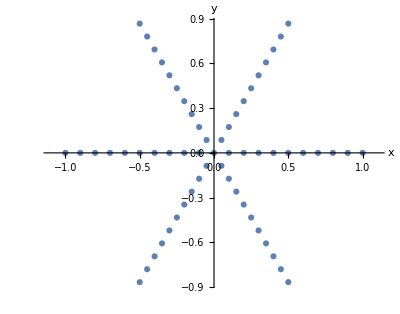

```mathematica
ListPlot[mesh["Coordinates"], PlotMarkers->Automatic,AxesLabel->{"x","y"},AspectRatio->Automatic,Joined->False,PlotRange->{{-1.1,1.1},All}]
```

```mathematica
Rock=<|"Young"-> 2.4,"Poisson"-> 0.2|>;
Ep=Rock["Young"]/(1-Rock["Poisson"]^2);
```

```mathematica
ker="2DP1"; 
ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={Rock["Young"],Rock["Poisson"]}; (* E, ν *) 
h1=toHMatExpr[mesh["Coordinates"],mesh["Connectivity"],ker,prop,ml,eta,eps];
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

```mathematica
h1
```

BigWhamLink`LTemplate`Classes`HMatExpr[1]

```mathematica
(* Unit Isotropic tensile loading *)
Pnet=1.;
LoadP1=ConstantArray[0., 4 Length[mesh["Connectivity"]]];
LoadP1[[2;;-1;;2]]=Pnet;
```

```mathematica
(* Solution via iterative Solve *)
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
{sol,stats}=Reap@LinearSolve[fdot,LoadP1,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-6.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
ds=sol[[1;;-1;;2]];dn=sol[[2;;-1;;2]];
Ntot=Nfracs Ne; 

Ndof=2;
opFrc= dn[[1+(Ndof Ne(#-1));;Ndof Ne #]]& /@ Range[Nfracs];
shFrc= ds[[1+(Ndof Ne(#-1));;Ndof Ne #]]& /@ Range[Nfracs];
```

```mathematica
Range[Nfracs]
```

{1,2,3,4,5,6}

```mathematica
coor=mesh["Coordinates"];
xb=(Flatten[coor[[#,1]]&/@mesh["Connectivity"][[1;;Ne]] ]);
opAllFrcs=Transpose[{xb,opFrc[[#]]}] & /@ Range[Nfracs];
shAllFrcs=Transpose[{xb,shFrc[[#]]}] & /@ Range[Nfracs];
```

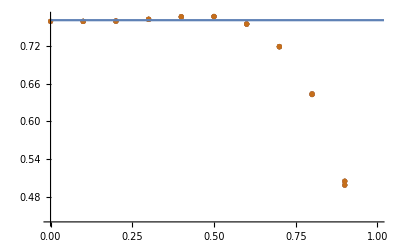

```mathematica
Show[ListPlot[ opAllFrcs],Plot[w0ref[Nfracs],{x,0,2}] ]
```

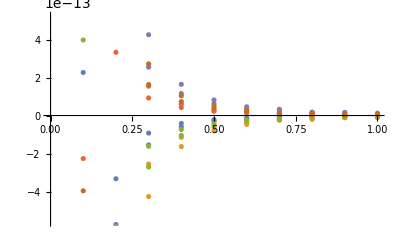

```mathematica
Show[ListPlot[ shAllFrcs] ]
```

```mathematica
hx=mesh["Coordinates"][[{1,2}]]//Differences //Norm
(* relative error on KI *)
relK1=1-KIfromDD[opAllFrcs[[1,{-2,-1},2]]//Mean,hx]/KIref[Nfracs]
(* relative error on KII *)
relK2= KIfromDD[shAllFrcs[[1,{-2,-1},2]]//Mean,hx]
```

0.1

0.0366954

-1.57529×10^-14

```mathematica
Volc=Total[#] hx /2&/@ opFrc;
W=Total[Volc] Pnet/2;
relWork=Abs[W-Wref[Nfracs] ]/ Wref[Nfracs]   (* relative error on total Elastic Work *)
relW0=(Abs[w0ref[Nfracs]-#[[1]] ]/w0ref[Nfracs]  & /@ opFrc )   //Mean (* relative error on center opening *)
```

0.00375116

0.00246848

```mathematica
LoadP1//Length
```

240

## S3DP0 kernel

Piece-wise constant DD

```mathematica
Ne=20;Nfracs=6;
```

```mathematica
mesh=CreateMeshStarCracks[Ne,Nfracs];
```

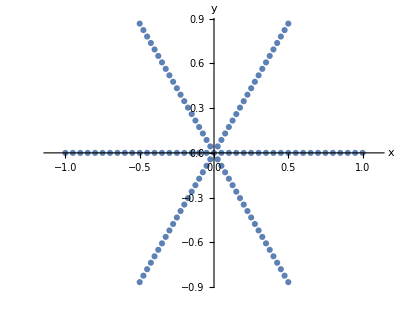

```mathematica
ListPlot[mesh["Coordinates"], PlotMarkers->Automatic,AxesLabel->{"x","y"},AspectRatio->Automatic,Joined->False,PlotRange->{{-1.1,1.1},All}]
```

```mathematica
Rock=<|"Young"-> 2.4,"Poisson"-> 0.2|>;
Ep=Rock["Young"]/(1-Rock["Poisson"]^2);
```

```mathematica
ker="S3DP0"; 
ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={Rock["Young"],Rock["Poisson"],1000.}; (* E, ν *) 
h1=toHMatExpr[mesh["Coordinates"],mesh["Connectivity"],ker,prop,ml,eta,eps];
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

```mathematica
(* Unit Isotropic tensile loading *)
Pnet=1.;
Load=ConstantArray[0., 2 Length[mesh["Connectivity"]]];
Load[[2;;-1;;2]]=Pnet;
```

```mathematica
(* Solution via iterative Solve *)
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
{sol,stats}=Reap@LinearSolve[fdot,Load,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-6.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
ds=sol[[1;;-1;;2]];dn=sol[[2;;-1;;2]];
Ntot=Nfracs Ne; 

Ndof=1;
opFrc= dn[[1+(Ndof Ne(#-1));;Ndof Ne #]]& /@ Range[Nfracs];
shFrc= ds[[1+(Ndof Ne(#-1));;Ndof Ne #]]& /@ Range[Nfracs];
```

```mathematica
Range[Nfracs]
```

{1,2,3,4,5,6}

```mathematica
coor=mesh["Coordinates"];
xb=(Flatten[Mean[coor[[#,1]]]&/@mesh["Connectivity"][[1;;Ne]] ]);
opAllFrcs=Transpose[{xb,opFrc[[#]]}] & /@ Range[Nfracs];
shAllFrcs=Transpose[{xb,shFrc[[#]]}] & /@ Range[Nfracs];
```

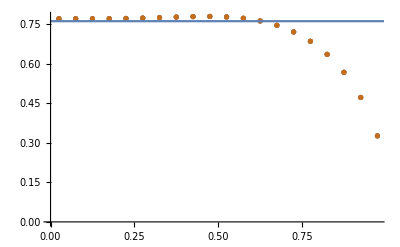

```mathematica
Show[ListPlot[ opAllFrcs],Plot[w0ref[Nfracs],{x,0,2}] ]
```

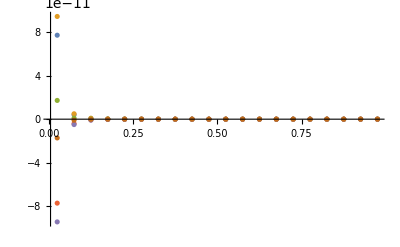

```mathematica
Show[ListPlot[ shAllFrcs,PlotRange->All] ]
```

```mathematica
hx=mesh["Coordinates"][[{1,2}]]//Differences //Norm;
(* relative error on KI *)
relK1=1-KIfromDD[opAllFrcs[[1,-1,2]],hx]/KIref[Nfracs]
(* relative error on KII  *)
relK2= KIfromDD[shAllFrcs[[1,-1,2]],hx]
```

-0.303117

1.00575×10^-14

```mathematica
Volc=Total[#] hx  &/@ opFrc;
W=Total[Volc] Pnet/2;
relWork=Abs[W-Wref[Nfracs] ]/ Wref[Nfracs]   (* relative error on total Elastic Work *)
relW0=(Abs[w0ref[Nfracs]-#[[1]] ]/w0ref[Nfracs]  & /@ opFrc )   //Mean (* relative error on center opening *)
```

0.0247054

0.0123154

```mathematica
Load//Length
```

240

## 2DP0 kernel

Piece-wise constant DD

```mathematica
Ne=20;Nfracs=6;
```

```mathematica
mesh=CreateMeshStarCracks[Ne,Nfracs];
```

```mathematica
ListPlot[mesh["Coordinates"], PlotMarkers->Automatic,AxesLabel->{"x","y"},AspectRatio->Automatic,Joined->False,PlotRange->{{-1.1,1.1},All}]
```

-Graphics-

```mathematica
Rock=<|"Young"-> 2.4,"Poisson"-> 0.2|>;
Ep=Rock["Young"]/(1-Rock["Poisson"]^2);
```

```mathematica
ker="2DP0"; 
ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={Rock["Young"],Rock["Poisson"]}; (* E, ν *) 
h1=toHMatExpr[mesh["Coordinates"],mesh["Connectivity"],ker,prop,ml,eta,eps];
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

```mathematica
(* Unit Isotropic tensile loading *)
Pnet=1.;
Load=ConstantArray[0., 2 Length[mesh["Connectivity"]]];
Load[[2;;-1;;2]]=Pnet;
```

```mathematica
(* Solution via iterative Solve *)
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
{sol,stats}=Reap@LinearSolve[fdot,Load,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-6.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
ds=sol[[1;;-1;;2]];dn=sol[[2;;-1;;2]];
Ntot=Nfracs Ne; 

Ndof=1;
opFrc= dn[[1+(Ndof Ne(#-1));;Ndof Ne #]]& /@ Range[Nfracs];
shFrc= ds[[1+(Ndof Ne(#-1));;Ndof Ne #]]& /@ Range[Nfracs];
```

```mathematica
Range[Nfracs]
```

{1,2,3,4,5,6}

```mathematica
coor=mesh["Coordinates"];
xb=(Flatten[Mean[coor[[#,1]]]&/@mesh["Connectivity"][[1;;Ne]] ]);
opAllFrcs=Transpose[{xb,opFrc[[#]]}] & /@ Range[Nfracs];
shAllFrcs=Transpose[{xb,shFrc[[#]]}] & /@ Range[Nfracs];
```

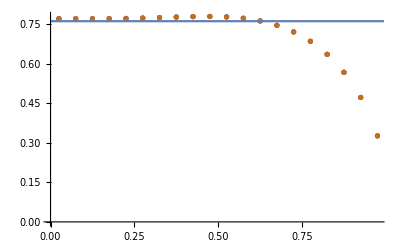

```mathematica
Show[ListPlot[ opAllFrcs],Plot[w0ref[Nfracs],{x,0,2}] ]
```

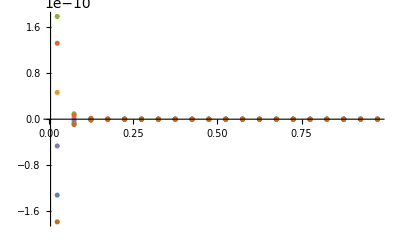

```mathematica
Show[ListPlot[ shAllFrcs,PlotRange->All] ]
```

```mathematica
hx=mesh["Coordinates"][[{1,2}]]//Differences //Norm;
(* relative error on KI *)
relK1=1-KIfromDD[opAllFrcs[[1,-1,2]],hx]/KIref[Nfracs]
(* relative error on KII  *)
relK2= KIfromDD[shAllFrcs[[1,-1,2]],hx]
```

-0.303133

-1.73537×10^-14

```mathematica
Volc=Total[#] hx  &/@ opFrc;
W=Total[Volc] Pnet/2;
relWork=Abs[W-Wref[Nfracs] ]/ Wref[Nfracs]   (* relative error on total Elastic Work *)
relW0=(Abs[w0ref[Nfracs]-#[[1]] ]/w0ref[Nfracs]  & /@ opFrc )   //Mean (* relative error on center opening *)
```

0.0247219

0.0123362

```mathematica
Load//Length
```

240